```mathematica
Clear["Global`*"];
```

#### Initialization

```mathematica
(* SET INTERVAL TO 1 BEFORE CHANGING INITIALIZATION PARAMETERS! *)

P           = 2;                      (* Laser Power [W] *)
nIndex           = 1.53;
P           = P (nIndex^2+1)/(2nIndex);
h           = 80;                      (* Heat Exchange Coefficient [W/m^2/K]*)
k           = 1.3;                 (* Thermal Conductivity [W/m/K] *)
c           = 854;                 (* Thermal Сapacity [J/kg/K] *)
rho       = 2165;                 (* Density [kg/m^3] *)
lx         = 42 10^-3;         (* X-size [m] *)
ly         = 5 10^-3;           (* Y-size [m] *)
lz         = 5 10^-3;           (* Z-size [m] *)
β     =5.6 10^-1;       (* Volume Absorption Coefficient [1/m] *)
S            = 14 10^-1;        (* Surface Absorption Coefficient [1/m] *)
t1          = 1000;                    (* Heating Stop Time [s] *)
α   =  k/c/rho;     (* [m^2/s] *)
H            = h/k;                (* [1/m] *)
A            = P/(k ly lz);(* [K/m] *)
(* HAVE YOU SET THE INTERVAL TO 1? *)

(*
Rest of variables and functions: rootsX [1/m], z [sqrt(m)], u [1/m], γ [1/m^2], P1,P2 and ψ [dimensionless], phi1 and phi2 [m^2]
*)
```

Configuration

```mathematica
numberOfTerms = 900; 
(*" 
Supposed number of terms in the series calculations.
Min(empiric): 900 terms for [interval = 5] Mode.
Good strategy to avoid weird mistakes: gradually increase the number of terms from ~5'000 to 30-40'000 with the step of 10'000.
Be patient: it is pretty long.
Caution: That's not a real number of terms because of duplicates. 
Check the lenght of rootsX to determine the number of terms in the final series calculation. 
"*)
interval = 5;
(*"
Supposed minimal interval between roots of the auxiliary equation (used to speed up the calculation).
Be careful: one lost root can spoil the solution.
Not sure about the value? Use interval = 1, then check the typical interval in the rootsX. Be patient: it is pretty long.
"*)
```

Auxiliary calculations
Auxiliary 1.xAxis
Trying to find non-zero roots of the auxiliary equation

```mathematica
Off[FindRoot::lstol]
rootsX=Table[x/.FindRoot[Tan[x lx]== (2 H x)/(x^2-H^2), {x, interval  i}],{i,0,numberOfTerms}];
```

```mathematica
rootsX=DeleteDuplicates[Round[rootsX,0.0000001]];
rootsX=Select[Chop[rootsX],#>0&];
rootsX
```

{44.8229,100.883,166.462,236.52,308.573,381.613,455.198,529.112,603.24,677.512,751.887,826.338,900.846,975.398,1049.99,1124.6,1199.24,1273.9,1348.57,1423.25,1497.95,1572.66,1647.37,1722.1,1796.83,1871.56,1946.3,2021.04,2095.79,2170.54,2245.3,2320.06,2394.82,2469.58,2544.35,2619.11,2693.88,2768.65,2843.42,2918.2,2992.97,3067.75,3142.53,3217.3,3292.08,3366.86,3441.64,3516.43,3591.21,3665.99,3740.77,3815.56,3890.34,3965.13,4039.92,4114.7,4189.49,4264.28,4339.07,4413.85,4488.64}

Auxiliary 1.yAxis

```mathematica
Off[FindRoot::lstol]
rootsY=Table[y/.FindRoot[Tan[y ly]== (2 H y)/(y^2-H^2), {y, interval  i}],{i,0,numberOfTerms}];
```

```mathematica
rootsY=DeleteDuplicates[Round[rootsY,0.0000001]];
rootsY=Select[Chop[rootsY],#>0&];
rootsY
```

{152.982,665.217,1275.91,1897.92,2523.03,3149.41,3776.43,4403.82}

Auxiliary 1.zAxis

```mathematica
Off[FindRoot::lstol]
rootsZ=Table[z/.FindRoot[Tan[z lz]== (2 H z)/(z^2-H^2), {z, interval * i}],{i,0,numberOfTerms}];
```

```mathematica
rootsZ=DeleteDuplicates[Round[rootsZ,0.0000001]];
rootsZ=Select[Chop[rootsZ],#>0&];
rootsZ
```

{152.982,665.217,1275.91,1897.92,2523.03,3149.41,3776.43,4403.82}

Auxiliary 2.xAxis

```mathematica
zX = ParallelTable[√(2/(2 H+lx(H^2+rootsX⟦i⟧^2))), {i, 1, Length[rootsX]}];
```

Auxiliary 2.yAxis

```mathematica
zY = ParallelTable[√(2/(2 H+ly(H^2+rootsY⟦i⟧^2))), {i, 1, Length[rootsY]}];
```

Auxiliary 2.zAxis

```mathematica
zZ = ParallelTable[√(2/(2 H+lz(H^2+rootsZ⟦i⟧^2))), {i, 1, Length[rootsZ]}];
```

Auxiliary 3

```mathematica
γ = Function[ {x,y,z}, x^2+ y^2 + z^2 ];
γ;
```

Auxiliary 4

```mathematica
P1 = ParallelTable[Sin[ lx * rootsX⟦i⟧ ]+ H/rootsX⟦i⟧(  1 - Cos[ lx rootsX⟦i⟧ ] ), {i, 1, Length[rootsX]}];
```

Auxiliary 5

```mathematica
P2 =ParallelTable[1/2( H * Sin[ lx*rootsX⟦i⟧ ] + rootsX⟦i⟧  (  1 + Cos[ lx*rootsX⟦i⟧ ] ) ), {i, 1, Length[rootsX]}];
```

Auxiliary 6

```mathematica
u = Function[{e,x}, e Cos[e x] + H Sin[e x]];
```

```mathematica
ψ[g_, t_] = Piecewise[{
{1 - Exp[-α* g * t], 0<t< t1},
{ (Exp[α* g * t1] - 1) Exp[-α* g * t], t>t1 }}];
```

Basic calculation

```mathematica
T[x_, y_, z_, t_] = P/k∑_(m=1)^Length[rootsX] ∑_(n=1)^Length[rootsY] ∑_(p=1)^Length[rootsZ] (zX⟦m⟧^2 zY⟦n⟧^2 zZ⟦p⟧^2)/γ[ rootsX⟦m⟧, rootsY⟦n⟧, rootsZ⟦p⟧ ] * 
u[rootsX⟦m⟧, x] u[rootsY⟦n⟧, y] u[rootsZ⟦p⟧, z](P1⟦m⟧ β + P2⟦m⟧S)u[rootsY⟦n⟧, ly/2] u[rootsZ⟦p⟧, lz/2]ψ[γ[rootsX⟦m⟧, rootsY⟦n⟧, rootsZ⟦p⟧ ], t];
```

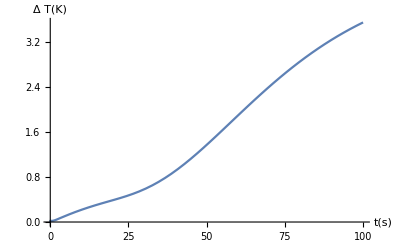

3904 terms were used in the series calculation.

```mathematica
Plot[
T[lx/2,ly/3,lz/50,  t], 
{t, 0, 100}, 
AxesLabel->{"t(s)", Style[ToExpression["\\Delta T (K)",TeXForm,HoldForm]]},
AxesStyle->Directive[Automatic, 14]  ]
Length[rootsX]Length[rootsY]Length[rootsZ]Text["terms were used in the series calculation." ]
```

1) [--, Слишком медленное суммирование ] Для динамических вычислений используются функции Dynamic, Manipulate и др.

2) Распределение в ly/2, lz/2 очень странное (в близких к ним точкам тоже самое), потому что там лазерный луч торчит именно в этой точке в сечении (луч бесконечно тонкий, так ставится задача). Хз, что с этим можно сделать.
Надо брать другие точки на сечении lx/2  (походить по сечению manipulate, вроде не должно меняться в зоне сечения либо усреднять как-то хитро придётся)

3) В ly/3, lz/3 наблюдается странный пик в момент выключения излучения (возможно артефакт вычислений, либо недостаток модели в смысле постановки задачи), но в области начального разогрева вроде как повторяет одномерную модель (если время отключения излучения отвести далеко от начала разогрева).
 Мало или много слагаемых -> ряд расходится (в комментах к одномерной также указать оптимальное количество слагаемых)
 Тут 3-4к слагаемых оптимально вроде (2к уже очень плохо, причем скачком)

4) Края? 
 Чем ближе к краю сечения, тем лучше 3х мерная повторяет одномерную модель (неважно к какому краю идти). Есть симметрия относительно центра сечения, т.е. значения в lz/5 и  4lz/5 совпадают при одинаковых lxCurrent и lyCurrent. Также проверил 2lz/5 и 3lz/5 (совпало). При движении от края, хвостик начала разогрева уверенно проваливается в отрицательную сторону. На ноль выходит где-то в районе 23/25 lz, а дальше начинает загибаться вверх.

```mathematica
(*Manipulate[  
Plot[
T[lx/2,ly/3,lzCurrent,  t], 
{t, 0, 100}, 
AxesLabel->{"t(s)", Style[ToExpression["\\Delta T (K)",TeXForm,HoldForm]]},
AxesStyle->Directive[Automatic, 14]  
],
{lzCurrent, 0, lz, 0.001}
 ]*)
```

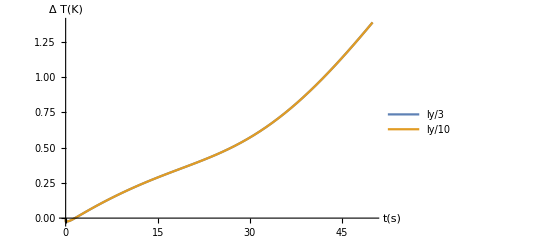

```mathematica
Plot[
{ Legended[ T[lx/2,ly/3,21 lz/25,  t], "ly/3"],
Legended[ T[lx/2,2ly/3,  4lz/25,  t], "ly/10"],
},
{t, 0, 50}, 
AxesLabel->{"t(s)", Style[ToExpression["\\Delta T (K)",TeXForm,HoldForm]]},
AxesStyle->Directive[Automatic, 14] ,
ImageSize-> Scaled[0.9]
]
```

```mathematica
(*Plot3D[
 Legended[ T[lx/2,lyCurrent,lzCurrent,  20], "ly/3"],
{lyCurrent, 0, ly}, 
{lzCurrent, 0, lz},
ImageSize-> Scaled[0.9],
PlotRange->Full
]*)
```

```mathematica
n=2;
grparallel=With[{rangeParts=Partition[Range[0,ly,ly/n],2,1]},ParallelCombine[Function[xrange,Plot3D[ T[lx/2,lyCurrent,lzCurrent,  20],Evaluate[{lyCurrent,First[xrange],Last[xrange]}],{lzCurrent,0,lz},BoundaryStyle->None,MaxRecursion->0]]/@#&,rangeParts,Show[{##},PlotRange->{0, 4}]&]];//AbsoluteTiming
```

General::munfl: Exp[-711.355] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-720.088] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.979] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{45.637,Null}

```mathematica
Show[grparallel, PlotRange->{0, 1.5}]
```

-Graphics3D-